# Multi-frequency Matter Perturbation

Prepare

```mathematica
imgsize=700;
```

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/GitHub/NeuPhysics/codebase/mma/matter

Conversions

```mathematica
ThetaMatter[thetav_,lambda_,omegav_:1]:=ArcTan[Sin[2thetav]/(Cos[2thetav]-lambda/omegav)]/2;
```

```mathematica
OmegaMatter[thetam_,thetav_,omegav_:1]:=omegav*Sqrt[Sin[thetav]^2+(Sin[2thetav]/Tan[2thetam])^2];
```

```mathematica
OmegaMatter2[lambda_,thetav_,omegav_:1]:=omegav*Sqrt[(lambda/omegav-Cos[2thetav])^2+Sin[2thetav]^2];
```

```mathematica
OmegaVacuum[energy_,deltam2_]:=deltam2/(2energy);(*input should be using the same units*)
```

```mathematica
MeVInverse2km[mev_]:=1.97*10^(-13)*(mev);(*  mev/1MeV=mev*(1/1MeV)=mev*(197fm)=...   *)
```

Parameters

```mathematica
gF=1.17*10^(-11)(*MeV^(-2)*)
ye=0.5
```

1.17×10^-11

0.5

```mathematica
deltamsquare13=2.6*10^(-15);(*MeV^2*)
energy10=10;(*Energy in units of MeV*)
omegaV=deltamsquare13/(2 energy10)(*MeV*);(*For 10 MeV neutrinos*)
thetaV=ArcSin[√0.093/2]
```

0.153077

```mathematica
fraction=10
lambdaN=fraction*Cos[2thetaV]omegaV
```

10

1.23955×10^-15

```mathematica
Cos[2thetaV]-(lambdaN/omegaV)^2
```

-89.9627

```mathematica
thetamV=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambdaN/omegaV)^2)]/2,Pi];
init={psi1[0],psi2[0]}=={1,0};
endpointN=1600;
```

Matter Profile

Hamiltonian

```mathematica
nNListTest={1,2,3,4,5,6}
nNListTestSym={n1,n2,n3,n4,n5,n6}
kNListTest={2.613874878374189273498126389572381489273897129879087581478947238946129836741984650871234,1.8,1.4,0.9,0.7,0.3}
kNListTestSym={k1,k2,k3,k4,k5,k6}
(*aNListTest=RandomReal[{0.000,0.200},6,WorkingPrecision->2]*lambdaN/OmegaMatter[thetamV,thetaV,omegaV]*)
aNListTest=0.1*kNListTest^(-5/3)
aNListTestSym={a1,a2,a3,a4,a5,a6}*lambdaN/OmegaMatter[thetamV,thetaV,omegaV]
phiNListTest={0,0,0,0,0,0}
```

{1,2,3,4,5,6}

{n1,n2,n3,n4,n5,n6}

{2.61387487837418927349812638957238148927389712987908758147894723894612983674198465087123,1.8,1.4,0.9,0.7,0.3}

{k1,k2,k3,k4,k5,k6}

{0.0201616,0.0375445,0.057076,0.119196,0.181205,0.743814}

{0.105988 a1,0.105988 a2,0.105988 a3,0.105988 a4,0.105988 a5,0.105988 a6}

{0,0,0,0,0,0}

```mathematica
nNListTest.kNListTest
nNListTestSym.kNListTestSym
```

19.3139

k1 n1+k2 n2+k3 n3+k4 n4+k5 n5+k6 n6

```mathematica
Total[nNListTest]
```

21

```mathematica
Table[BesselJ[aNListTest[[n]]/kNListTest[[n]] Cos[2thetamV],nNListTest[[n]]],{n,1,6}]
Times@@Table[BesselJ[aNListTestSym[[n]]/kNListTestSym[[n]] Cos[2thetamV],nNListTestSym[[n]]],{n,1,6}]
```

{0.766215,0.240444,-0.235516,-0.392322,-0.283909,-0.0807571}

BesselJ[(0.105988 a1)/k1,n1] BesselJ[(0.105988 a2)/k2,n2] BesselJ[(0.105988 a3)/k3,n3] BesselJ[(0.105988 a4)/k4,n4] BesselJ[(0.105988 a5)/k5,n5] BesselJ[(0.105988 a6)/k6,n6]

```mathematica
hNtest[aNList_,kNList_,phiNList_,nNList_,thetam_,x_]:=Module[{thetamM,BNM,phiNListM,kNListM,aNListM,nNListM,length,PhiNM,gNM},
thetamM=thetam;
nNListM=nNList;
kNListM=kNList;
aNListM=aNList;
length=Length@kNListM;
phiNListM=phiNList;

gNM=nNListM.kNListM ;
BNM=(-I)^(Total[nNListM])Tan[2thetamM] gNM Times@@Table[BesselJ[nNListM[[n]],aNListM[[n]]/kNListM[[n]] Cos[2thetamM]],{n,1,length}];
PhiNM=Exp[I nNListM.phiNListM];


1/2{{0,-BNM PhiNM Exp[I (gNM-1) x]},{-Conjugate[BNM] Conjugate[PhiNM] Exp[-I (gNM-1) x],0}}
]
```

Generate test lists

```mathematica
k3ListTest={1.18,0.73,0.37};
a3ListTest=0.02k3ListTest^(-5/3);
phi3ListTest={0,0,0};
n3ListTest={1,1,1};
```

```mathematica
hNtest[a3ListTest,k3ListTest,phi3ListTest,n3ListTest,thetamV,x]
```

{{0,(0.+7.97485×10^-8 ⅈ) ⅇ^((0.+1.28 ⅈ) x)},{(0.-7.97485×10^-8 ⅈ) ⅇ^((0.-1.28 ⅈ) x),0}}

```mathematica
solNList[listInput_,aNList_,kNList_,phiNList_,thetam_,endpoint_]:=Module[
{listInputM,aNListM,kNListM,phiNListM,thetamM,length,endpointM,hamilM,initM},

thetamM=thetam;
listInputM=listInput;
aNListM=aNList;
kNListM=kNList;
phiNListM=phiNList;
length=Length@listInputM;
endpointM=endpoint;
initM={psi1[0],psi2[0]}=={1,0};


hamilM=Total@Table[hNtest[aNListM,kNListM,phiNListM,listInputM[[i]],thetamM,x],{i,1,length}];

NDSolve[I D[{psi1[x],psi2[x]},x]==hamilM.{psi1[x],psi2[x]}&&initM,{psi1,psi2},{x,0,endpointM}]

]
```

```mathematica
listInputTest={{1,1,1},{1,2,1}}
```

{{1,1,1},{1,2,1}}

```mathematica
solNList[listInputTest,a3ListTest,k3ListTest,phi3ListTest,thetamV,endpointN]
```

{{psi1→InterpolatingFunction[{{0., 1600.}}, <>],psi2→InterpolatingFunction[{{0., 1600.}}, <>]}}

```mathematica
pltNList[listInput_,aNList_,kNList_,phiNList_,thetam_,endpoint_,legends_,color_,frameTicks_,frameLabel_,startpoint_:0]:=Plot[Evaluate[Abs[psi2[x]]^2/.solNList[listInput,aNList,kNList,phiNList,thetam,endpoint]],{x,startpoint,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x",frameLabel}},PlotStyle->color,PlotLegends->Placed[Style[ToString[legends],color],{Top,Center}],FrameTicks->{{Automatic,None},{Automatic,frameTicks}},PlotPoints->endpoint]
```

```mathematica
pltNList[listInputTest,a3ListTest,k3ListTest,phi3ListTest,thetamV,endpointN/10,"Approximation",Blue,None,None]
```

-Graphics-

```mathematica
(Total@Table[aNListTest[[i]]Sin[kNListTest[[i]]x+phiNListTest[[i]]],{i,1,Length@kNListTest}])Exp[I(-x-Cos[2thetam]( 
Total@Table[aNListTest[[i]]/kNListTest[[i]] Cos[kNListTest[[i]]x+phiNListTest[[i]]],{i,1,Length@kNListTest}]
 ))]
```

ⅇ^(ⅈ (-x-Cos[2 thetam] (2.47938 Cos[0.3 x]+0.258864 Cos[0.7 x]+0.13244 Cos[0.9 x]+0.0407685 Cos[1.4 x]+0.020858 Cos[1.8 x]+0.00771331 Cos[2.61387487837418927349812638957238148927389712987908758147894723894612983674198465087123 x]))) (0.743814 Sin[0.3 x]+0.181205 Sin[0.7 x]+0.119196 Sin[0.9 x]+0.057076 Sin[1.4 x]+0.0375445 Sin[1.8 x]+0.0201616 Sin[2.61387487837418927349812638957238148927389712987908758147894723894612983674198465087123 x])

```mathematica
solNN[aNList_,kNList_,phiNList_,thetam_,endpoint_]:=Module[
{listInputM,aNListM,kNListM,phiNListM,thetamM,length,endpointM,hamilM,hamil12M,hamil21M,initM,maxstepsValueM},

thetamM=thetam;
aNListM=aNList;
kNListM=kNList;
phiNListM=phiNList;
length=Length@listInputM;
endpointM=endpoint;
initM={psi1[0],psi2[0]}=={1,0};
maxstepsValueM=11000000000;

hamil12M=Sin[2thetamM]/2(Total@Table[aNListM[[i]]Sin[kNListM[[i]]x+phiNListM[[i]]],{i,1,Length@kNListM}])Exp[I(-x-Cos[2thetam]( 
Total@Table[aNListM[[i]]/kNListM[[i]] Cos[kNListM[[i]]x+phiNListM[[i]]],{i,1,Length@kNListM}]
 ))];
hamil21M=Sin[2thetamM]/2(Total@Table[aNListM[[i]]Sin[kNListM[[i]]x+phiNListM[[i]]],{i,1,Length@kNListM}])Exp[-I(-x-Cos[2thetam]( 
Total@Table[aNListM[[i]]/kNListM[[i]] Cos[kNListM[[i]]x+phiNListM[[i]]],{i,1,Length@kNListM}]
 ))];

NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,hamil12M},{hamil21M,0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpointM},MaxSteps->maxstepsValueM]

]
```

```mathematica
pltNN[aNList_,kNList_,phiNList_,thetam_,endpoint_,pltLabel_,color_,frameTicks_,frameLabel_,startpoint_:0]:=Plot[Evaluate[Abs[psi2[x]]^2/.solNN[aNList,kNList,phiNList,thetam,endpoint][[1]]],{x,startpoint,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x",frameLabel}},PlotStyle->color,PlotLegends->Placed[Style[pltLabel,color],{Top,Center}],FrameTicks->{{Automatic,None},{Automatic,frameTicks}},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18},ImagePadding->{{Automatic,Automatic},{Automatic,60}}(*,PlotPoints->endpoint-startpoint*)]
```

```mathematica
solNN[a3ListTest,k3ListTest,phi3ListTest,thetamV,endpointN/10]
```

{{psi1→InterpolatingFunction[{{0., 160.}}, <>],psi2→InterpolatingFunction[{{0., 160.}}, <>]}}

```mathematica
pltNN[a3ListTest,k3ListTest,phi3ListTest,thetamV,endpointN/10,"Numerical;",Blue,None,None]
```

-Graphics-

```mathematica
Show[
pltNN[a3ListTest,k3ListTest,phi3ListTest,thetamV,endpointN/10,"Numerical",{Red,Dashed},None,None],pltNList[listInputTest,a3ListTest,k3ListTest,phi3ListTest,thetamV,endpointN/10,"Approximation",Blue,None,None],PlotRange->All
]
```

-Graphics-

### Test 2 frequency

```mathematica
thetamVn2Test=Pi/5;
thetaVn2Test=ArcSin[√0.3/2];
omegaVn2Test=3.75*10^(-17);
k2ListTest={0.3,0.7};
k2ListTestSym={k1,k2};
a2ListTest={0.1,0.1};
a2ListTestSym={a1,a2};
phi2ListTest={0,0};
n2ListTest={3,3};
n2ListTestSym={n1,n2};
n2ListInputTest={{1,1},{0,1},{1,0},{-1,0},{0,-1},{2,0}}
```

{{1,1},{0,1},{1,0},{-1,0},{0,-1},{2,0}}

```mathematica
hNtest[a2ListTestSym,k2ListTestSym,phi2ListTest,n2ListTestSym,thetamVn2Test,x]
```

{{0,-1/2 (-ⅈ)^(n1+n2) √(5+2 √5) ⅇ^(ⅈ (-1+k1 n1+k2 n2) x) (k1 n1+k2 n2) BesselJ[n1,((-1+√5) a1)/(4 k1)] BesselJ[n2,((-1+√5) a2)/(4 k2)]},{-1/2 √(5+2 √5) ⅇ^(-ⅈ (-1+k1 n1+k2 n2) x) Conjugate[(-ⅈ)^(n1+n2) (k1 n1+k2 n2) BesselJ[n1,((-1+√5) a1)/(4 k1)] BesselJ[n2,((-1+√5) a2)/(4 k2)]],0}}

```mathematica
hNtest[a2ListTest,k2ListTest,phi2ListTest,n2ListTest,thetamVn2Test,x]
```

{{0,1.88247×10^-10 ⅇ^((0.+2. ⅈ) x)},{1.88247×10^-10 ⅇ^((0.-2. ⅈ) x),0}}

```mathematica
pltNList[n2ListInputTest,a2ListTest,k2ListTest,phi2ListTest,thetamVn2Test,endpointN,"TEST",Blue,None,None]
```

-Graphics-

```mathematica
pltNN[a2ListTest,k2ListTest,phi2ListTest,thetamVn2Test,endpointN,"Numerical",{Red,Dashed},None,None]
```

-Graphics-

```mathematica
Show[
pltNList[n2ListInputTest,a2ListTest,k2ListTest,phi2ListTest,thetamVn2Test,endpointN,"TEST",Blue,None,None],pltNN[a2ListTest,k2ListTest,phi2ListTest,thetamVn2Test,endpointN,"Numerical",{Red,Thickness[0.005],Dashing[{0.004,0.03}]},None,None],PlotRange->All
]
```

-Graphics-

Calculate the qvalues

```mathematica
listNGeneratorTest[nRangeList_]:=Module[{lengthM,tableRangeM},
lengthM=Length@nRangeList;

Table[
Table[i,{i,-nRangeList[[j]],nRangeList[[j]]}],
{j,1,lengthM}
]

]
```

```mathematica
listNGeneratorTest[{3,3,3}]
```

{{-3,-2,-1,0,1,2,3},{-3,-2,-1,0,1,2,3},{-3,-2,-1,0,1,2,3}}

```mathematica
listNGeneratorTest2[lengthOfList_,rangeOfElement_]:=Module[{},

Table[{-rangeOfElement,rangeOfElement},
{j,1,lengthOfList}
]

]
```

```mathematica
listNGeneratorTest2[6,3]
```

{{-3,3},{-3,3},{-3,3},{-3,3},{-3,3},{-3,3}}

```mathematica
bCoefN[listOfN_,listOfWaveNumber_,listOfAmplitude_,listOfPhase_,thetam_]:=
-(-I)^(Total[listOfN]) Tan[2thetam]/2 (listOfN.listOfWaveNumber) Apply[Times,MapThread[BesselJ[#1,#3/#2 Cos[2thetam]]&,{listOfN,listOfWaveNumber,listOfAmplitude}]];

distanceN[listOfN_,listOfWaveNumber0_]:=Abs[listOfN.listOfWaveNumber0-1];

qValue[listOfN_,listOfWaveNumber_,listOfAmplitude_,listOfPhase_,thetam_]:=distanceN[listOfN,listOfWaveNumber]/Abs[bCoefN[listOfN,listOfWaveNumber,listOfAmplitude,listOfPhase,thetam]];

qValueOrderdList[listOfNRange_,listOfWaveNumber_,listOfAmplitude_,listOfPhase_,thetam_]:=Module[{maptolist,listOfThreadM},

listOfThreadM=Tuples[Table[Table[ni,{ni,listOfNRange[[n,1]],listOfNRange[[n,2]]}],{n,1,Length@listOfNRange}]];

SortBy[
Table[{listN,qValue[listN,listOfWaveNumber,listOfAmplitude,listOfPhase,thetam]},{listN,listOfThreadM}]//Quiet
,Last]

]
```

```mathematica
testQList=qValueOrderdList[listNGeneratorTest2[6,3],kNListTest,aNListTest,phiNListTest,thetamV];
```

```mathematica
testQList[[200]]
```

{{0,0,0,0,-2,-1},227814.}

```mathematica
Grid@Part[qValueOrderdList[listNGeneratorTest2[6,3],kNListTest,aNListTest,phiNListTest,thetamV],1;;20]
```

{0,-3,1,3,2,3} | 0.
{0,-2,1,3,2,-3} | 0.
{0,-2,2,3,0,-3} | 0.
{0,-1,0,2,1,1} | 0.
{0,-1,0,3,1,-2} | 0.
{0,-1,1,1,2,-3} | 0.
{0,-1,1,2,-1,1} | 0.
{0,-1,2,1,0,-3} | 0.
{0,0,-2,2,2,2} | 0.
{0,0,-1,2,0,2} | 0.
{0,0,0,0,1,1} | 0.
{0,0,0,1,1,-2} | 0.
{0,0,0,2,-2,2} | 0.
{0,0,1,-1,2,-3} | 0.
{0,0,1,0,-1,1} | 0.
{0,0,2,-1,0,-3} | 0.
{0,0,2,1,-3,-2} | 0.
{0,1,-2,0,2,2} | 0.
{0,1,-1,0,0,2} | 0.
{0,1,0,-2,1,1} | 0.

```mathematica
(*Flatten[ Drop[Part[qValueOrderdList[listNGeneratorTest2[6,3],kNListTest,aNListTest,phiNListTest,thetamV],1;;10],None,{2}],1];*)
```

### Solving a 6 frequency problem as an example

Some test on the q values. In principle, we need to include q value up to 1. However, as I’ll show in the following, we actually need to include q value up to at least several hundred.

```mathematica
qValueOrderedListTest1=qValueOrderdList[listNGeneratorTest2[6,4],kNListTest,aNListTest,phiNListTest,thetamV]
```

{{{0,-3,1,3,2,3},0.},{{0,-3,1,4,2,0},0.},{{0,-2,0,3,1,4},0.},{{0,-2,0,3,4,-3},0.},{{0,-2,0,4,1,1},0.},531431,{{0,2,-1,-3,2,-3},ComplexInfinity},{{0,2,0,-4,0,0},ComplexInfinity},{{0,2,0,-3,0,-3},ComplexInfinity},{{0,2,1,-4,-2,0},ComplexInfinity},{{0,2,1,-3,-2,-3},ComplexInfinity}}
 |  |  |  |

```mathematica
qValueOrderedListTest1[[200]]
```

{{0,-3,3,1,1,2},660.97}

```mathematica
Abs[{-3,3,-1,3,4,-2}.kNListTest-1]
```

0.0583754

```mathematica
distanceN[{-3,3,-1,3,4,-2},kNListTest]
```

0.0583754

```mathematica
Abs[bCoefN[{-3,3,-1,3,4,-2},kNListTest,aNListTest,phiNListTest,thetamV]]
```

1.63028×10^-29

```mathematica
pltNList[{{-3,3,-1,3,4,-2}},aNListTest,kNListTest,phiNListTest,thetamV,endpointN,"TEST",Blue]
```

Now solve the equations

```mathematica
solNList[Flatten[ Drop[Part[qValueOrderdList[listNGeneratorTest2[6,3],kNListTest,aNListTest,phiNListTest,thetamV],1;;10],None,{2}],1],aNListTest,kNListTest,phiNListTest,thetamV,endpointN]
```

{{psi1→InterpolatingFunction[{{0., 1600.}}, <>],psi2→InterpolatingFunction[{{0., 1600.}}, <>]}}

```mathematica
pltNListTicksFull=Table[{x,ScientificForm[MeVInverse2km[x/OmegaMatter[thetamV,thetaV,omegaV]],2]},{x,0,endpointN/10}];
```

```mathematica
pltNListTicks=Take[pltNListTicksFull,{1,Length@pltNListTicksFull,Floor[(Length@pltNListTicksFull)/5]}];
```

```mathematica
pltNListTicks
```

{{0,0.},{32,5.4×10^2},{64,1.1×10^3},{96,1.6×10^3},{128,2.2×10^3},{160,2.7×10^3}}

```mathematica
pltNListApprox1=pltNList[Flatten[ Drop[Part[qValueOrderdList[listNGeneratorTest2[6,4],kNListTest,aNListTest,phiNListTest,thetamV],1;;200],None,{2}],1],aNListTest,kNListTest,phiNListTest,thetamV,endpointN/10,"Approximation;",Blue,pltNListTicks,"Distance (km)"]
```

-Graphics-

```mathematica
pltNListNum1=pltNN[aNListTest,kNListTest,phiNListTest,thetamV,endpointN/10,"Numerical;",{Red,Dashed},pltNListTicks,"Distance (km)"]
```

-Graphics-

```mathematica
Show[pltNListNum1,pltNListApprox1,Graphics[Text["6 frequencies\n 10λ_MSW\n 200 Combinations",ImageScaled[{0.3,0.7}]]]
]
```

-Graphics-

Understand Interference?

Use two frequencies
k1=0.999, k2=0.3
1. Complete numerical
2. Test approximations

```mathematica
onekList={0.999};
twokList={0.999,0.6};
oneaList={0.1};
twoaList={0.1,0.1};
onephiList={0};
twophiList={0,0};
threekList={0.999,0.6,0.4};
threeaList={0.1,0.1,0.1};
threephiList={0,0,0};
thetaVRes=thetaV;
thetamVRes=thetamV;
omegaVRes=omegaV;
endpointNRes=endpointN*15
```

24000

```mathematica
oneListFullTicks=Table[{x,ScientificForm[MeVInverse2km[x/OmegaMatter[thetamVRes,thetaVRes,omegaVRes]],2]},{x,0,endpointNRes}];
```

```mathematica
oneListTicks=Take[oneListFullTicks,{1,Length@oneListFullTicks,Floor[(Length@oneListFullTicks)/5]}];
```

```mathematica
oneListTicks
```

{{0,0.},{4800,8.1×10^4},{9600,1.6×10^5},{14400,2.4×10^5},{19200,3.2×10^5},{24000,4.×10^5}}

```mathematica
oneNPlt=pltNN[oneaList,onekList,onephiList,thetamVRes,endpointNRes,"Single Frequency",{Red,Dashed},oneListTicks,"Distance (km)"];
```

```mathematica
oneListPlt=pltNList[{{1}},oneaList,onekList,onephiList,thetamVRes,endpointNRes,"Single Frequency",Blue,oneListTicks,"Distance (km)"];
```

```mathematica
twoNPlt=pltNN[twoaList,twokList,twophiList,thetamVRes,endpointNRes,"Two Frequencies",{Red,Dashed},oneListTicks,"Distance (km)"];
```

```mathematica
twoEffectiveList=Flatten[ Drop[Part[qValueOrderdList[listNGeneratorTest2[2,4],twokList,twoaList,twophiList,thetamVRes],1;;2],None,{2}],1]
```

qValueOrderdList[listNGeneratorTest2[2],{0.999}]

```mathematica
twoListPlt=pltNList[twoEffectiveList,twoaList,twokList,twophiList,thetamVRes,endpointNRes,"Approximation;",Blue,oneListTicks,"Distance (km)"];
```

Part::partw: Part 2 of listNGeneratorTest2[2] does not exist.

Part::partw: Part 2 of listNGeneratorTest2[2.] does not exist.

Dot::dotsh: Tensors {0.999} and {0.999, 0.6} have incompatible shapes.

Part::partw: Part 2 of {0.999} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Dot::dotsh: Tensors {0.999} and {0, 0} have incompatible shapes.

Dot::dotsh: Tensors {0.999} and {0., 0.} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at x == 0..

ReplaceAll::reps: NDSolve[{ⅈ SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00100104 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{ⅈ SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00100104 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{(0.`  + 1.` ⅈ) SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 1.00104 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

```mathematica
threeNPlt=pltNN[threeaList,threekList,threephiList,thetamVRes,endpointNRes,"Three Frequencies Numerical",{Red,Dashed},oneListTicks,"Distance (km)"];
```

```mathematica
threeEffectiveList=Flatten[ Drop[Part[qValueOrderdList[listNGeneratorTest2[3,4],threekList,threeaList,threephiList,thetamVRes],1;;4],None,{2}],1]
```

qValueOrderdList[listNGeneratorTest2[3],{0.999,0.4},{0.1,0.1},{0,0}]

```mathematica
threeListPlt=pltNList[{threeEffectiveList[[2]],threeEffectiveList[[4]]},threeaList,threekList,threephiList,thetamVRes,endpointNRes,"Approximation;",Blue,oneListTicks,"Distance (km)"];
```

Dot::dotsh: Tensors {0.999, 0.4} and {0.999, 0.6, 0.4} have incompatible shapes.

Part::partw: Part 3 of {0.999, 0.4} does not exist.

Dot::dotsh: Tensors {0.999, 0.4} and {0, 0, 0} have incompatible shapes.

Dot::dotsh: Tensors {0, 0} and {0.999, 0.6, 0.4} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 3 of {0, 0} does not exist.

Part::partw: Part 3 of {0., 0.} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at x == 0..

ReplaceAll::reps: NDSolve[{ⅈ SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00100104 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{ⅈ SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00100104 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{(0.`  + 1.` ⅈ) SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 1.00104 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

```mathematica
(*Grid[{{Show[oneListPlt,oneNPlt,GridLines->Automatic]},{Show[twoListPlt,twoNPlt,GridLines->Automatic]},{Show[threeListPlt,threeNPlt,GridLines->Automatic]}}]*)
```

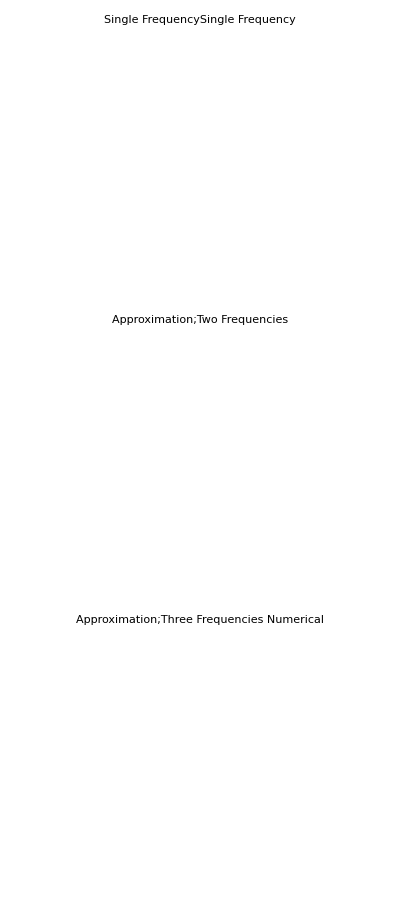

```mathematica
Grid[{{Show[oneListPlt,oneNPlt]},{Show[twoListPlt,twoNPlt]},{Show[threeListPlt,threeNPlt]}}]
```

### Can we just linearly add up all the oscillations from each combinations of n’s?

For two frequency case, we have the useful combination to be

```mathematica
twoEffectiveList
```

{{1,0},{0,1}}

Now we grab the each one and make lists of transition probabilities

```mathematica
twoListData[listInput_,aNList_,kNList_,phiNList_,thetam_,endpoint_,step_:1,startpoint_:0]:=Table[Evaluate[psi2[x]/.First@solNList[listInput,aNList,kNList,phiNList,thetam,endpoint]],{x,startpoint,endpoint,step}];
(*MapThread[{#1,#2}&,
{Table[x,{x,startpoint,endpoint,step}],
Table[Evaluate[Abs[psi2[x]]^2/.First@solNList[listInput,aNList,kNList,phiNList,thetam,endpoint]],{x,startpoint,endpoint,step}]}
]*)
```

```mathematica
twoListDatax=Table[x,{x,0,endpointNRes,100}];
twoListData1=twoListData[{twoEffectiveList[[1]]},twoaList,twokList,twophiList,thetamVRes,endpointNRes,100];
twoListData2=twoListData[{twoEffectiveList[[2]]},twoaList,twokList,twophiList,thetamVRes,endpointNRes,100];
```

Part::partw: Part 2 of listNGeneratorTest2[2] does not exist.

Part::partw: Part 2 of listNGeneratorTest2[2.] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at x == 0..

ReplaceAll::reps: {ⅈ SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Dot::dotsh: Tensors {0.999} and {0.999, 0.6} have incompatible shapes.

Part::partw: Part 2 of {0.999} does not exist.

Dot::dotsh: Tensors {0.999} and {0, 0} have incompatible shapes.

Dot::dotsh: Tensors {0.999} and {0., 0.} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at x == 0..

ReplaceAll::reps: {ⅈ SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
listPltNList[listData_,legends_,color_,frameTicks_,frameLabel_]:=ListPlot[listData,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x",frameLabel}},PlotStyle->color,PlotLegends->Placed[Style[ToString[legends],color],{Top,Center}],FrameTicks->{{Automatic,None},{Automatic,frameTicks}}]
```

```mathematica
twoListData1Plt=listPltNList[MapThread[{#1,Abs[#2]^2}&,{twoListDatax,twoListData1}],"List 1;",Magenta,oneListTicks,"Distance (km)"]
twoListData2Plt=listPltNList[MapThread[{#1,Abs[#2]^2}&,{twoListDatax,twoListData2}],"List 2;",Magenta,oneListTicks,"Distance (km)"]
```

Part::partw: Part 2 of listNGeneratorTest2[2] does not exist.

Part::partw: Part 2 of listNGeneratorTest2[2.] does not exist.

ReplaceAll::reps: {ⅈ SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 2 of listNGeneratorTest2[2.] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

Dot::dotsh: Tensors {0.999} and {0., 0.} have incompatible shapes.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Dot::dotsh: Tensors {0.999} and {0., 0.} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

-Graphics-

```mathematica
Show[twoListData1Plt,twoNPlt]
```

-Graphics-

Two frequencies doens’t really help us. Should check three frequencies.

```mathematica
threeEffectiveList
```

{{0,-1,4},{0,1,1},{0,3,-2},{1,0,0}}

```mathematica
threeListDatax=Table[x,{x,0,endpointNRes,100}];
threeListDataFull=Table[
twoListData[{threeEffectiveList[[i]]},threeaList,threekList,threephiList,thetamVRes,endpointNRes,100]
,{i,1,Length@threeEffectiveList}];
threeListData1=twoListData[{threeEffectiveList[[1]]},threeaList,threekList,threephiList,thetamVRes,endpointNRes,100];
threeListData2=twoListData[{threeEffectiveList[[2]]},threeaList,threekList,threephiList,thetamVRes,endpointNRes,100];
threeListData3=twoListData[{threeEffectiveList[[3]]},threeaList,threekList,threephiList,thetamVRes,endpointNRes,100];
threeListData4=twoListData[{threeEffectiveList[[4]]},threeaList,threekList,threephiList,thetamVRes,endpointNRes,100];
```

```mathematica
threeListData=Total@threeListDataFull;
threeListDataTemp=threeListData2+threeListData4;
```

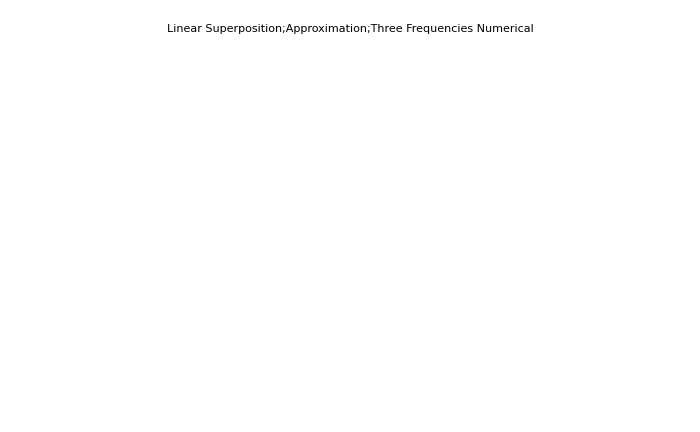

```mathematica
Show[listPltNList[MapThread[{#1,Abs[#2]^2}&,{threeListDatax,threeListData}],"Linear Superposition;",Magenta,oneListTicks,"Distance (km)"],threeListPlt,threeNPlt]
```

```mathematica
qValueOrderdList[listNGeneratorTest2[3,4],threekList,threeaList,threephiList,thetamVRes]
```

{{{0,-1,4},0.},{{0,1,1},0.},{{0,3,-2},1.77592×10^-7},{{1,0,0},12.2284},{{0,1,0},4880.47},{{0,0,1},7288.7},{{0,0,-1},17007.},{{0,0,2},19386.},{{0,-1,0},19521.9},{{-1,0,0},24444.6},{{1,0,1},27654.6},{{0,2,0},29249.1},{{1,1,0},54724.9},{{1,0,-1},64912.7},{{2,-1,-1},92817.4},{{0,-1,-1},116214.},{{-1,0,-1},166274.},{{0,0,-2},174474.},{{1,1,-1},192450.},{{1,-1,0},220043.},{{0,1,-1},232429.},{{-1,-1,0},237446.},{{2,0,0},243734.},{{-1,0,1},258842.},{{0,1,2},264942.},{{1,-1,1},291698.},{{0,0,3},309773.},{{0,-2,0},321740.},{{0,2,-1},348242.},{{0,-1,1},348643.},{{-1,2,2},443148.},{{-1,1,0},512214.},{{0,2,1},522362.},{{1,1,1},579477.},{{1,0,2},687253.},{{-2,0,0},732180.},{{2,0,-1},1.44938×10^6},{{0,-1,-2},1.58965×10^6},{{2,-1,0},1.66123×10^6},{{-1,-1,-1},1.73959×10^6},{{1,2,0},1.90946×10^6},{{-1,-1,1},2.12662×10^6},{{2,0,1},2.25796×10^6},{{0,-2,-1},2.26357×10^6},{{-1,0,-2},2.40753×10^6},{{-1,1,-1},2.61077×10^6},{{0,3,0},2.8063×10^6},{{1,-1,2},3.07119×10^6},{{0,-2,1},3.13417×10^6},{{0,0,-3},3.4075×10^6},{{2,1,0},3.58914×10^6},{{0,-1,2},3.70919×10^6},{{1,1,-2},4.65502×10^6},{{-1,-2,0},5.09455×10^6},{{-2,0,-1},5.48824×10^6},{{0,1,-2},5.56378×10^6},{{1,0,-2},6.22845×10^6},{{-2,0,1},6.29682×10^6},{{-2,-1,0},8.08118×10^6},{{-1,0,2},9.32324×10^6},{{0,-3,0},9.82206×10^6},{{0,1,3},9.87833×10^6},{{-2,1,0},1.00091×10^7},{{2,0,-2},1.02154×10^7},{{1,-2,3},1.0643×10^7},{{1,2,-3},1.0643×10^7},{{1,1,2},1.07909×10^7},{{0,2,2},1.11147×10^7},{{1,2,-1},1.23455×10^7},{{-1,2,0},1.39209×10^7},{{0,3,-1},1.43194×10^7},{{0,-1,3},1.48175×10^7},{{1,2,1},1.71016×10^7},{{-1,2,1},1.84541×10^7},{{3,0,0},1.9485×10^7},{{1,0,3},2.02228×10^7},{{2,-1,1},2.05562×10^7},{{1,-2,0},2.09249×10^7},{{0,0,4},2.22863×10^7},{{2,1,-1},2.52441×10^7},{{-1,-1,-2},2.62176×10^7},{{0,3,1},2.73371×10^7},{{-1,1,2},2.76411×10^7},{{2,1,1},3.0867×10^7},{{-1,3,0},3.13034×10^7},{{0,-2,-2},3.33442×10^7},{{0,2,-2},3.33442×10^7},{{-1,1,-2},3.39374×10^7},{{0,-1,-3},3.45742×10^7},{{2,-2,0},3.54088×10^7},{{-1,-2,-1},3.84919×10^7},{{-3,0,0},3.89994×10^7},{{2,0,2},3.97182×10^7},{{-1,-1,2},4.16636×10^7},{{-1,-2,1},4.3248×10^7},{{-1,4,-1},4.79409×10^7},{{-1,0,-3},5.39557×10^7},{{0,1,-3},5.927×10^7},{{-2,-1,-1},6.17648×10^7},{{1,-1,-2},6.46496×10^7},{{-2,-1,1},6.73877×10^7},{{-2,1,-1},7.20756×10^7},{{0,-3,-1},7.2899×10^7},{{1,-2,-1},7.40476×10^7},{{0,-2,2},7.78032×10^7},{{1,3,0},8.09839×10^7},{{-2,0,-2},8.38986×10^7},{{0,-3,1},8.59167×10^7},{{-2,1,1},9.27246×10^7},{{2,2,0},9.61419×10^7},{{0,0,-4},9.65742×10^7},{{-1,1,3},1.10189×10^8},{{1,-2,1},1.11885×10^8},{{-2,0,2},1.13401×10^8},{{1,2,-2},1.26514×10^8},{{3,0,-1},1.42732×10^8},{{-1,0,3},1.47434×10^8},{{3,0,1},1.6378×10^8},{{1,-1,3},1.66149×10^8},{{-1,3,1},1.67379×10^8},{{-1,2,-1},1.67479×10^8},{{-1,-3,0},1.71016×10^8},{{0,4,0},1.76737×10^8},{{2,-2,1},1.83505×10^8},{{-2,-2,0},1.83623×10^8},{{3,-1,0},2.03803×10^8},{{1,0,-3},2.21613×10^8},{{3,1,0},2.52472×10^8},{{1,-3,0},2.83303×10^8},{{1,1,3},2.85068×10^8},{{1,2,2},2.95678×10^8},{{1,-2,2},2.96961×10^8},{{-3,0,-1},3.00433×10^8},{{0,2,3},3.10809×10^8},{{-2,2,0},3.15174×10^8},{{-3,0,1},3.21481×10^8},{{2,1,-2},3.28044×10^8},{{2,0,-3},3.7501×10^8},{{0,1,4},3.87648×10^8},{{2,-1,2},4.02854×10^8},{{0,-4,0},4.29217×10^8},{{-3,-1,0},4.46905×10^8},{{0,3,2},4.92186×10^8},{{-3,1,0},4.95574×10^8},{{2,-1,-2},4.96871×10^8},{{2,1,2},5.21608×10^8},{{1,3,-1},5.83223×10^8},{{-1,-2,-2},5.91504×10^8},{{-1,-1,-3},6.01985×10^8},{{1,1,-3},6.68069×10^8},{{1,3,1},6.87478×10^8},{{2,2,-1},7.13481×10^8},{{-1,1,-3},7.20904×10^8},{{1,0,4},7.29631×10^8},{{0,-2,-3},7.54821×10^8},{{-1,-2,2},7.60668×10^8},{{-1,0,4},7.87335×10^8},{{2,2,1},8.01712×10^8},{{1,-2,-2},8.86739×10^8},{{-2,-1,-2},9.56644×10^8},{{1,-1,-3},9.97242×10^8},{{2,0,3},1.01823×10^9},{{0,-1,-4},1.03373×10^9},{{-2,1,-2},1.0754×10^9},{{0,-3,-2},1.10742×10^9},{{2,1,-4},1.13522×10^9},{{-2,-1,2},1.15021×10^9},{{-1,1,1},1.15837×10^9},{{1,-1,-1},1.16069×10^9},{{-1,2,-2},1.18414×10^9},{{0,4,-1},1.20242×10^9},{{2,-3,2},1.27756×10^9},{{-1,-3,-1},1.31274×10^9},{{3,-1,-1},1.38572×10^9},{{-1,-3,1},1.417×10^9},{{-2,-2,-1},1.41889×10^9},{{0,1,-4},1.42138×10^9},{{-1,3,-1},1.49393×10^9},{{-2,-2,1},1.50712×10^9},{{0,4,1},1.54597×10^9},{{-1,-1,3},1.55512×10^9},{{0,-3,2},1.5996×10^9},{{-1,0,-4},1.64224×10^9},{{2,-2,-1},1.6794×10^9},{{-1,4,0},1.73049×10^9},{{4,0,0},1.75198×10^9},{{3,-1,1},1.78326×10^9},{{1,-3,-1},1.83284×10^9},{{3,1,-1},1.90742×10^9},{{-2,0,-3},1.94473×10^9},{{-2,1,2},1.97512×10^9},{{3,0,-2},2.01809×10^9},{{-2,2,-1},2.0371×10^9},{{3,1,1},2.08119×10^9},{{-1,1,4},2.37348×10^9},{{3,0,2},2.72852×10^9},{{-4,0,0},2.92153×10^9},{{-1,2,3},3.04324×10^9},{{1,0,-4},3.15921×10^9},{{3,-2,-2},3.19509×10^9},{{0,-4,-1},3.26372×10^9},{{-2,0,3},3.33796×10^9},{{-3,-1,-1},3.47004×10^9},{{1,-3,1},3.49415×10^9},{{0,-4,1},3.60727×10^9},{{-3,-1,1},3.6438×10^9},{{2,3,0},3.70774×10^9},{{3,-2,0},3.71794×10^9},{{-3,1,-1},3.76796×10^9},{{-2,2,1},3.9×10^9},{{-3,1,1},4.1655×10^9},{{1,4,0},4.26719×10^9},{{-3,0,-2},4.67956×10^9},{{2,1,-3},5.04362×10^9},{{-3,0,2},5.39×10^9},{{-1,3,2},5.99127×10^9},{{-2,-3,0},6.35802×10^9},{{3,2,0},6.38551×10^9},{{2,-2,2},6.63061×10^9},{{1,-1,4},7.08737×10^9},{{1,2,3},7.50428×10^9},{{-1,-4,0},7.82467×10^9},{{1,3,-2},7.97607×10^9},{{1,1,4},9.74862×10^9},{{2,2,-2},1.03297×10^10},{{1,-4,0},1.03614×10^10},{{-3,-2,0},1.03802×10^10},{{2,-1,3},1.08969×10^10},{{0,2,4},1.09523×10^10},{{1,3,2},1.15255×10^10},{{0,3,3},1.27802×10^10},{{0,3,-3},1.27802×10^10},{{-3,2,0},1.30478×10^10},{{2,1,3},1.30515×10^10},{{2,2,2},1.32867×10^10},{{4,0,-1},1.33899×10^10},{{-1,-2,-3},1.37605×10^10},{{4,0,1},1.43285×10^10},{{0,4,-2},1.43915×10^10},{{3,-1,-2},1.65583×10^10},{{1,-2,-3},1.82215×10^10},{{-1,-1,-4},1.8615×10^10},{{3,-2,-1},1.89088×10^10},{{4,-1,0},1.97153×10^10},{{2,-3,0},2.03857×10^10},{{-1,-3,-2},2.03947×10^10},{{-1,2,-3},2.12754×10^10},{{-1,-2,3},2.12754×10^10},{{-1,1,-4},2.12763×10^10},{{-1,4,1},2.13432×10^10},{{4,1,0},2.18637×10^10},{{-2,-2,-2},2.21505×10^10},{{-2,-1,-3},2.23806×10^10},{{-4,0,-1},2.2767×10^10},{{0,-2,-4},2.31214×10^10},{{-4,0,1},2.37056×10^10},{{-1,-3,2},2.39442×10^10},{{-2,1,-3},2.45351×10^10},{{-2,-2,2},2.51075×10^10},{{0,-2,4},2.55553×10^10},{{0,-3,-3},2.55605×10^10},{{1,-3,-2},2.5929×10^10},{{1,-1,-4},2.59902×10^10},{{0,4,2},2.63845×10^10},{{2,-3,1},2.68546×10^10},{{2,3,-1},2.81916×10^10},{{3,1,-2},2.84579×10^10},{{-2,2,-2},2.88066×10^10},{{-2,-1,3},3.03884×10^10},{{2,3,1},3.0432×10^10},{{3,-1,2},3.04393×10^10},{{-2,3,0},3.04515×10^10},{{-2,3,3},3.04995×10^10},{{1,4,-1},3.19872×10^10},{{-4,-1,0},3.40238×10^10},{{2,0,4},3.42047×10^10},{{3,1,2},3.42205×10^10},{{1,4,1},3.53569×10^10},{{-4,1,0},3.61722×10^10},{{3,-2,1},3.62521×10^10},{{3,0,-3},3.93762×10^10},{{3,2,-1},4.90141×10^10},{{-2,-3,-1},4.94638×10^10},{{3,-3,0},4.96384×10^10},{{0,-4,-2},5.03703×10^10},{{0,-3,3},5.11209×10^10},{{-2,-3,1},5.17042×10^10},{{3,2,1},5.20637×10^10},{{-3,-1,-2},5.4368×10^10},{{-3,1,-2},5.81492×10^10},{{0,2,-4},5.9629×10^10},{{-3,-1,2},6.01306×10^10},{{-2,0,-4},6.05362×10^10},{{-1,-4,-1},6.06208×10^10},{{0,-4,2},6.23633×10^10},{{-1,-4,1},6.39905×10^10},{{3,0,3},6.76281×10^10},{{2,0,-4},7.16508×10^10},{{2,-1,-3},7.17588×10^10},{{-3,1,2},7.20301×10^10},{{1,-4,-1},7.46345×10^10},{{-3,-2,-1},8.10121×10^10},{{-3,-2,1},8.40617×10^10},{{1,-4,1},9.59298×10^10},{{-3,2,-1},9.68237×10^10},{{1,-2,4},9.69612×10^10},{{-2,3,-1},1.0675×10^11},{{-2,1,3},1.07191×10^11},{{-3,0,-3},1.09935×10^11},{{-3,2,1},1.14167×10^11},{{-3,0,3},1.38187×10^11},{{1,3,-3},1.43305×10^11},{{4,-1,-1},1.47768×10^11},{{-1,2,4},1.51203×10^11},{{0,4,-3},1.5331×10^11},{{-2,3,1},1.57814×10^11},{{4,-1,1},1.6337×10^11},{{-2,0,4},1.66392×10^11},{{4,1,-1},1.6894×10^11},{{3,-1,-3},1.7473×10^11},{{4,1,1},1.77405×10^11},{{2,4,0},1.86585×10^11},{{-1,3,3},1.91368×10^11},{{4,0,-2},2.03378×10^11},{{2,2,-3},2.12135×10^11},{{2,-2,3},2.12135×10^11},{{1,2,-4},2.27594×10^11},{{4,0,2},2.34275×10^11},{{2,-3,-1},2.3771×10^11},{{3,3,0},2.38735×10^11},{{1,2,4},2.50482×10^11},{{-4,-1,-1},2.66196×10^11},{{-4,-1,1},2.7466×10^11},{{-4,1,-1},2.8023×10^11},{{1,3,3},2.86885×10^11},{{-4,1,1},2.95832×10^11},{{-2,-4,0},2.96406×10^11},{{2,2,3},3.28129×10^11},{{3,-4,1},3.45654×10^11},{{-4,0,-2},3.57708×10^11},{{-2,4,0},3.5924×10^11},{{-3,-3,0},3.64484×10^11},{{2,-1,4},3.77522×10^11},{{-4,0,2},3.88605×10^11},{{-1,4,2},4.1788×10^11},{{-2,3,2},4.21472×10^11},{{2,3,-2},4.24861×10^11},{{-1,-2,-4},4.29462×10^11},{{4,-2,0},4.30293×10^11},{{2,1,4},4.31534×10^11},{{0,3,4},4.32688×10^11},{{1,4,-2},4.71163×10^11},{{-2,4,1},4.73236×10^11},{{-1,-3,-3},4.78206×10^11},{{2,3,2},4.98855×10^11},{{-1,4,-2},5.08425×10^11},{{-2,-2,-3},5.2126×10^11},{{1,-2,-4},5.2874×10^11},{{4,2,0},5.40956×10^11},{{-3,3,0},5.53581×10^11},{{1,-3,-3},5.73723×10^11},{{1,-3,3},5.76216×10^11},{{-1,2,-4},5.82982×10^11},{{1,4,2},5.83441×10^11},{{3,-3,-1},6.09762×10^11},{{3,1,-3},6.18761×10^11},{{-1,-3,3},6.21786×10^11},{{-2,2,3},6.31759×10^11},{{-2,-2,3},6.37254×10^11},{{-2,2,-3},6.37254×10^11},{{3,-2,2},6.52966×10^11},{{0,4,3},6.64345×10^11},{{-2,-1,-4},7.01411×10^11},{{3,2,-2},7.49256×10^11},{{-2,1,-4},7.55423×10^11},{{3,-1,3},7.66525×10^11},{{-2,-3,-2},7.76151×10^11},{{0,-3,-4},7.93262×10^11},{{-4,-2,0},7.98799×10^11},{{3,0,-4},8.06734×10^11},{{3,1,3},8.4036×10^11},{{2,-4,0},8.42232×10^11},{{3,2,2},8.49342×10^11},{{-2,-3,2},8.50146×10^11},{{3,-3,1},8.94936×10^11},{{-1,-2,4},9.07537×10^11},{{-4,2,0},9.09462×10^11},{{-1,-4,-2},9.48206×10^11},{{-1,-4,2},1.06048×10^12},{{1,-4,-2},1.11377×10^12},{{-2,-1,4},1.13408×10^12},{{0,-4,-3},1.17538×10^12},{{-3,-2,-2},1.27433×10^12},{{-2,3,-2},1.27628×10^12},{{-3,-1,-3},1.283×10^12},{{-1,3,-3},1.34131×10^12},{{-3,1,-3},1.35684×10^12},{{-3,-2,2},1.37442×10^12},{{2,4,-1},1.43739×10^12},{{-3,2,-2},1.47071×10^12},{{2,-2,-3},1.48115×10^12},{{-3,-1,3},1.5046×10^12},{{2,4,1},1.51734×10^12},{{0,-4,3},1.68641×10^12},{{2,-3,-2},1.69648×10^12},{{3,3,-1},1.84953×10^12},{{3,3,1},1.93334×10^12},{{-3,1,3},1.94863×10^12},{{1,3,-4},2.03016×10^12},{{1,-4,2},2.04007×10^12},{{-3,2,2},2.12687×10^12},{{4,-1,-2},2.1761×10^12},{{3,0,4},2.22127×10^12},{{-2,1,4},2.23785×10^12},{{-2,-4,-1},2.31635×10^12},{{-2,-4,1},2.3963×10^12},{{0,3,-4},2.4519×10^12},{{4,1,-2},2.60712×10^12},{{4,-1,2},2.69601×10^12},{{-3,-3,-1},2.85464×10^12},{{4,1,2},2.88361×10^12},{{-3,-3,1},2.93845×10^12},{{1,-3,4},3.07713×10^12},{{4,-2,-1},3.09793×10^12},{{-2,2,4},3.35259×10^12},{{2,-1,-4},3.37079×10^12},{{-3,0,-4},3.45634×10^12},{{4,-2,1},3.65341×10^12},{{0,-3,4},3.67785×10^12},{{-3,3,-1},3.89305×10^12},{{-4,-1,-2},4.19553×10^12},{{4,2,-1},4.20843×10^12},{{2,-4,-1},4.30692×10^12},{{2,-3,3},4.35017×10^12},{{4,2,1},4.36692×10^12},{{-4,1,-2},4.38313×10^12},{{-4,-1,2},4.47202×10^12},{{4,0,-3},4.55718×10^12},{{-3,0,4},4.87088×10^12},{{-4,1,2},4.90304×10^12},{{2,2,-4},5.08176×10^12},{{-2,4,2},5.1407×10^12},{{-3,3,1},5.39774×10^12},{{4,0,3},5.72919×10^12},{{-4,-2,-1},6.26723×10^12},{{-4,-2,1},6.42572×10^12},{{-4,2,-1},6.98074×10^12},{{-1,3,4},7.13744×10^12},{{0,4,-4},7.35319×10^12},{{-4,2,1},7.53622×10^12},{{2,-2,4},7.91676×10^12},{{-4,0,-3},8.45997×10^12},{{3,-1,-4},8.64659×10^12},{{-2,2,2},8.84158×10^12},{{2,-2,-2},8.87701×10^12},{{2,3,-3},9.3987×10^12},{{1,3,4},9.45134×10^12},{{-4,0,3},9.63198×10^12},{{3,-4,0},9.76942×10^12},{{1,4,-3},1.00085×10^13},{{2,2,4},1.07494×10^13},{{-1,4,3},1.12987×10^13},{{3,4,0},1.17908×10^13},{{2,3,3},1.2223×10^13},{{4,-3,0},1.31265×10^13},{{-1,-1,4},1.41677×10^13},{{1,1,-4},1.4196×10^13},{{1,4,3},1.43646×10^13},{{-1,-3,-4},1.50126×10^13},{{-1,3,-2},1.59442×10^13},{{1,-3,2},1.59761×10^13},{{-2,-2,-4},1.641×10^13},{{3,1,-4},1.69482×10^13},{{3,-2,3},1.69588×10^13},{{3,2,-3},1.69588×10^13},{{-3,-4,0},1.71539×10^13},{{3,-2,-3},1.71805×10^13},{{1,-3,-4},1.73265×10^13},{{-2,-3,-3},1.83375×10^13},{{3,-3,2},1.90734×10^13},{{-2,2,-4},1.92426×10^13},{{4,3,0},1.99434×10^13},{{3,2,3},2.07352×10^13},{{-2,-3,3},2.11618×10^13},{{0,4,4},2.20596×10^13},{{-2,-2,4},2.20776×10^13},{{2,4,-2},2.20878×10^13},{{-1,-4,-3},2.23472×10^13},{{-1,-3,4},2.24338×10^13},{{2,4,2},2.47048×10^13},{{1,-4,-3},2.54132×10^13},{{3,-1,4},2.54542×10^13},{{-2,3,-3},2.62103×10^13},{{-1,-4,3},2.67033×10^13},{{3,1,4},2.74153×10^13},{{-1,3,-4},2.75411×10^13},{{-4,-3,0},2.82601×10^13},{{3,3,-2},2.8646×10^13},{{-3,-2,-3},3.01668×10^13},{{2,-2,-4},3.05119×10^13},{{2,-3,-3},3.053×10^13},{{3,3,2},3.13784×10^13},{{-3,-2,3},3.39432×10^13},{{-3,2,-3},3.39432×10^13},{{-4,3,0},3.50771×10^13},{{-2,-4,-2},3.64746×10^13},{{0,-4,-4},3.67659×10^13},{{-3,4,0},3.87141×10^13},{{-2,-4,2},3.90916×10^13},{{-3,-1,-4},4.04796×10^13},{{4,-2,-2},4.23409×10^13},{{-3,1,-4},4.24407×10^13},{{-3,-3,-2},4.503×10^13},{{4,-1,-3},4.62058×10^13},{{2,-4,2},4.62689×10^13},{{-3,-3,2},4.77624×10^13},{{-3,-1,4},5.09467×10^13},{{2,-4,-2},5.60387×10^13},{{-3,3,-2},5.7335×10^13},{{3,-3,-2},5.8028×10^13},{{4,1,-3},5.98573×10^13},{{4,-2,2},6.12556×10^13},{{4,2,-2},6.55498×10^13},{{0,-4,4},6.61787×10^13},{{4,-1,3},6.63801×10^13},{{-3,2,3},6.80825×10^13},{{4,1,3},7.02019×10^13},{{4,2,2},7.07004×10^13},{{-1,4,-3},7.29671×10^13},{{-3,1,4},7.65415×10^13},{{4,-3,-1},8.47877×10^13},{{3,4,-1},9.18841×10^13},{{3,4,1},9.50565×10^13},{{-4,-2,-2},9.90032×10^13},{{-4,-1,-3},9.94771×10^13},{{-4,1,-3},1.03299×10^14},{{-4,-2,2},1.04154×10^14},{{-2,4,-2},1.07448×10^14},{{-4,2,-2},1.08448×10^14},{{1,-4,3},1.09679×10^14},{{-4,-1,3},1.09822×10^14},{{4,-3,1},1.17613×10^14},{{-4,1,3},1.23473×10^14},{{-4,2,2},1.27363×10^14},{{4,0,-4},1.32172×10^14},{{-3,3,2},1.34436×10^14},{{-3,-4,-1},1.34688×10^14},{{-3,-4,1},1.37861×10^14},{{-2,3,4},1.40094×10^14},{{4,3,-1},1.55852×10^14},{{4,3,1},1.60429×10^14},{{2,-4,3},1.85597×10^14},{{4,0,4},1.86312×10^14},{{2,-3,4},2.16848×10^14},{{-4,-3,-1},2.2218×10^14},{{-4,-3,1},2.26758×10^14},{{-3,4,-1},2.3009×10^14},{{1,4,-4},2.60678×10^14},{{-4,3,-1},2.64997×10^14},{{2,3,-4},2.663×10^14},{{-4,0,-4},2.67388×10^14},{{-2,4,3},2.75522×10^14},{{4,-3,-3},2.93875×10^14},{{-4,3,1},2.97822×10^14},{{-4,0,4},3.21529×10^14},{{-1,4,4},3.91354×10^14},{{2,3,4},3.98075×10^14},{{4,-4,0},4.31872×10^14},{{3,-4,-1},4.68236×10^14},{{1,4,4},4.69524×10^14},{{3,2,-4},5.00439×10^14},{{2,4,-3},5.03932×10^14},{{3,-4,2},5.20952×10^14},{{3,-3,3},5.33687×10^14},{{3,-2,4},5.74236×10^14},{{-2,-3,-4},5.79101×10^14},{{2,4,3},6.02225×10^14},{{3,3,-3},6.61135×10^14},{{3,2,4},6.73417×10^14},{{-3,4,1},6.97981×10^14},{{-1,-4,-4},7.04344×10^14},{{-2,-3,4},7.10875×10^14},{{4,-2,-3},7.5949×10^14},{{-2,3,-4},7.60328×10^14},{{3,3,3},7.63016×10^14},{{1,-4,-4},7.82513×10^14},{{2,-3,-4},8.37082×10^14},{{-2,-4,-3},8.64176×10^14},{{4,-3,-2},8.66013×10^14},{{-1,-4,4},9.13189×10^14},{{-3,-2,-4},9.54183×10^14},{{-2,4,-1},9.56505×10^14},{{2,-4,1},9.60339×10^14},{{-2,-4,3},9.62469×10^14},{{4,4,0},9.75675×10^14},{{-3,2,-4},1.05336×10^15},{{-3,-3,-3},1.06841×10^15},{{-3,-2,4},1.12716×10^15},{{-3,-3,3},1.17029×10^15},{{2,-4,-3},1.19088×10^15},{{4,-1,-4},1.20231×10^15},{{-3,3,-3},1.29773×10^15},{{-4,-4,0},1.3373×10^15},{{3,4,-2},1.4344×10^15},{{4,-4,-1},1.50433×10^15},{{4,-2,3},1.52484×10^15},{{4,2,-3},1.52484×10^15},{{3,4,2},1.53736×10^15},{{-2,4,-3},1.652×10^15},{{4,2,3},1.71582×10^15},{{4,1,-4},1.8073×10^15},{{-4,4,0},1.88111×10^15},{{4,-3,2},2.03392×10^15},{{-3,-4,-2},2.12899×10^15},{{4,-1,4},2.16977×10^15},{{-3,-4,2},2.23195×10^15},{{4,1,4},2.27493×10^15},{{-4,-2,-3},2.35178×10^15},{{1,-4,4},2.36248×10^15},{{4,3,-2},2.44184×10^15},{{-4,2,-3},2.54276×10^15},{{-4,-2,3},2.54276×10^15},{{4,3,2},2.59007×10^15},{{-3,4,-2},3.1454×10^15},{{-4,-1,-4},3.15058×10^15},{{-4,1,-4},3.25574×10^15},{{-4,2,3},3.30811×10^15},{{3,-2,-4},3.31717×10^15},{{-4,-3,-2},3.51576×10^15},{{-1,4,-4},3.53635×10^15},{{-4,-1,4},3.61822×10^15},{{-4,-3,2},3.66399×10^15},{{2,-4,4},3.87475×10^15},{{-4,3,-2},4.07191×10^15},{{-3,4,4},4.20227×10^15},{{-4,1,4},4.2232×10^15},{{4,-4,1},4.58055×10^15},{{-3,2,4},4.94477×10^15},{{-4,3,2},5.23982×10^15},{{-3,4,2},7.19724×10^15},{{4,4,-1},7.64856×10^15},{{4,4,1},7.82878×10^15},{{-4,-4,-1},1.05302×10^16},{{4,-2,-4},1.06573×10^16},{{-4,-4,1},1.07104×10^16},{{3,-4,-2},1.08636×10^16},{{-2,4,4},1.17338×10^16},{{-4,4,-1},1.37784×10^16},{{2,4,-4},1.50653×10^16},{{-4,4,1},1.68547×10^16},{{3,-3,4},1.88116×10^16},{{3,-4,3},1.94877×10^16},{{2,4,4},1.95355×10^16},{{3,3,-4},2.01214×10^16},{{3,3,4},2.47029×10^16},{{-2,-4,-4},2.73529×10^16},{{-3,4,3},2.89284×10^16},{{-2,-4,4},3.18231×10^16},{{3,4,-3},3.34699×10^16},{{-3,-3,-4},3.38572×10^16},{{2,-4,-4},3.51546×10^16},{{3,4,3},3.72786×10^16},{{4,-4,-2},3.75426×10^16},{{-3,-3,4},3.84386×10^16},{{-3,3,-4},3.97484×10^16},{{-2,4,-4},4.30137×10^16},{{-3,3,4},4.33751×10^16},{{4,2,-4},4.69468×10^16},{{4,-2,4},5.02379×10^16},{{-3,-4,-3},5.05996×10^16},{{4,-3,3},5.16275×10^16},{{-3,-4,3},5.44083×10^16},{{4,2,4},5.54621×10^16},{{4,3,-3},5.72534×10^16},{{4,3,3},6.27153×10^16},{{-3,4,-3},6.83905×10^16},{{-4,-2,-4},7.46002×10^16},{{-4,2,-4},7.98244×10^16},{{-4,-2,4},8.31154×10^16},{{-4,-3,-3},8.36344×10^16},{{4,-4,2},8.53505×10^16},{{-4,-3,3},8.90963×10^16},{{-4,3,-3},9.47222×10^16},{{3,-3,-4},1.01935×10^17},{{3,-4,-3},1.16807×10^17},{{-4,2,4},1.19405×10^17},{{4,4,-2},1.20312×10^17},{{4,4,2},1.26133×10^17},{{-4,3,3},1.46644×10^17},{{-4,-4,-2},1.66847×10^17},{{-4,-4,2},1.72667×10^17},{{-4,4,-2},2.07629×10^17},{{-3,3,3},3.04321×10^17},{{3,-3,-3},3.06153×10^17},{{-4,4,2},3.30522×10^17},{{3,-4,4},7.6547×10^17},{{3,4,-4},1.03494×10^18},{{3,4,4},1.20417×10^18},{{4,-3,-4},1.58602×10^18},{{-3,-4,-4},1.60576×10^18},{{4,-3,4},1.7234×10^18},{{-3,-4,4},1.77498×10^18},{{4,3,-4},1.78216×10^18},{{4,3,4},2.02342×10^18},{{-3,4,-4},2.04445×10^18},{{4,-4,3},2.2554×10^18},{{-4,-3,-4},2.65614×10^18},{{3,-4,-4},2.80572×10^18},{{4,4,-3},2.83544×10^18},{{-4,-3,4},2.8974×10^18},{{-4,3,-4},2.95616×10^18},{{4,4,3},3.04895×10^18},{{-4,-4,-3},3.97344×10^18},{{-4,-4,3},4.18694×10^18},{{-4,4,-3},4.76699×10^18},{{4,-4,-3},5.35546×10^18},{{-4,3,4},6.26558×10^18},{{-4,4,3},1.23778×10^19},{{4,-4,4},7.71424×10^19},{{4,4,-4},8.88617×10^19},{{4,4,4},9.82301×10^19},{{-4,-4,-4},1.26312×10^20},{{-4,-4,4},1.3568×10^20},{{-4,4,-4},1.474×10^20},{{-4,4,4},2.79555×10^22},{{4,-4,-4},2.818×10^22},{{0,-2,3},2.39959×10^24},{{0,2,-3},2.39959×10^24},{{0,0,0},ComplexInfinity}}

```mathematica
pltNList[{threeEffectiveList[[1]]},threeaList,threekList,threephiList,thetamVRes,endpointNRes,"Approximation;",Blue,oneListTicks,"Distance (km)"]
pltNList[{threeEffectiveList[[4]]},threeaList,threekList,threephiList,thetamVRes,endpointNRes,"List 4;",Blue,oneListTicks,"Distance (km)"]
pltNList[{threeEffectiveList[[2]]},threeaList,threekList,threephiList,thetamVRes,endpointNRes,"List 2;",Blue,oneListTicks,"Distance (km)"]
pltNList[{threeEffectiveList[[3]]},threeaList,threekList,threephiList,thetamVRes,endpointNRes,"List 3;",Blue,oneListTicks,"Distance (km)"]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
widthN[listOfN_,listOfWaveNumber_,listOfAmplitude_,listOfPhase_,thetam_]:=Abs[
-(-I)^(Total[listOfN]) Tan[2thetam]/2 (listOfN.listOfWaveNumber) Apply[Times,MapThread[BesselJ[#1,#3/#2 Cos[2thetam]]&,{listOfN,listOfWaveNumber,listOfAmplitude}]]
];
```

```mathematica
Table[widthN[threeEffectiveList[[i]],threekList,threeaList,threephiList,thetamVRes],{i,1,4}]
```

{1.40709×10^-9,0.0000172096,1.25031×10^-9,0.0000817769}

TEMP

```mathematica
sysTemp=D[D[psi2[x],x],x]+I(n k - 1)D[psi2[x],x]+1/4 Bn*Conjugate[Bn] psi2[x]==0
```

1/4 Bn Conjugate[Bn] psi2[x]+ⅈ (-1+k n) psi2'[x]+psi2''[x]==0

```mathematica
DSolve[sysTemp&&psi2[0]==0&&psi2'[0]==-I/2 Conjugate[Bn]Exp[-I(n k-1)x],psi2,x]//FullSimplify
```

{{psi2→Function[{x},-((ⅈ ⅇ^(-ⅈ (-1+k n) x-1/2 ⅈ x (-1+k n-ⅈ √(-1+2 k n-k^2 n^2-Bn Conjugate[Bn]))) (-1+ⅇ^(1/2 ⅈ x (-1+k n-ⅈ √(-1+2 k n-k^2 n^2-Bn Conjugate[Bn]))+1/2 x (-ⅈ (-1+k n)+√(-1+2 k n-k^2 n^2-Bn Conjugate[Bn])))) Conjugate[Bn])/(2 √(-1+2 k n-k^2 n^2-Bn Conjugate[Bn])))]}}

```mathematica
ⅇ^(-ⅈ (-1+k n) x-1/2 ⅈ x (-1+k n-ⅈ √(-1+2 k n-k^2 n^2-Bn Conjugate[Bn]))) //FullSimplify
```

ⅇ^(-1/2 x (-3 ⅈ+3 ⅈ k n+√(-(-1+k n)^2-Bn Conjugate[Bn])))

```mathematica
ⅇ^(1/2 ⅈ x (-1+k n-ⅈ √(-1+2 k n-k^2 n^2-Bn Conjugate[Bn]))+1/2 x (-ⅈ (-1+k n)+√(-1+2 k n-k^2 n^2-Bn Conjugate[Bn])))//FullSimplify
```

ⅇ^(x √(-(-1+k n)^2-Bn Conjugate[Bn]))

```mathematica
sysTemp2=I D[{psi1[x],psi2[x]},x]==1/2{{0,Bn Exp[I(n k -1)x]},{Bn2 Exp[-I(n k -1)x],0}}.{psi1[x],psi2[x]}
```

{ⅈ psi1'[x],ⅈ psi2'[x]}=={1/2 Bn ⅇ^(ⅈ (-1+k n) x) psi2[x],1/2 Bn2 ⅇ^(-ⅈ (-1+k n) x) psi1[x]}

```mathematica
DSolve[sysTemp2&&{psi1[0],psi2[0]}=={1,0},{psi1,psi2},x]
```

{{psi1→Function[{x},1/(2 √(-1-Bn Bn2+2 k n-k^2 n^2))(-ⅈ ⅇ^(1/2 ⅈ (-1+k n+ⅈ √(-1-Bn Bn2+2 k n-k^2 n^2)) x)+ⅈ ⅇ^(1/2 (ⅈ (-1+k n)+√(-1-Bn Bn2+2 k n-k^2 n^2)) x)+ⅈ ⅇ^(1/2 ⅈ (-1+k n+ⅈ √(-1-Bn Bn2+2 k n-k^2 n^2)) x) k n-ⅈ ⅇ^(1/2 (ⅈ (-1+k n)+√(-1-Bn Bn2+2 k n-k^2 n^2)) x) k n+ⅇ^(1/2 ⅈ (-1+k n+ⅈ √(-1-Bn Bn2+2 k n-k^2 n^2)) x) √(-1-Bn Bn2+2 k n-k^2 n^2)+ⅇ^(1/2 (ⅈ (-1+k n)+√(-1-Bn Bn2+2 k n-k^2 n^2)) x) √(-1-Bn Bn2+2 k n-k^2 n^2))],psi2→Function[{x},1/(2 Bn √(-1-Bn Bn2+2 k n-k^2 n^2))ⅇ^(-ⅈ (-1+k n) x) (ⅇ^(1/2 ⅈ (-1+k n+ⅈ √(-1-Bn Bn2+2 k n-k^2 n^2)) x)-ⅇ^(1/2 (ⅈ (-1+k n)+√(-1-Bn Bn2+2 k n-k^2 n^2)) x)) (-1+k n-ⅈ √(-1-Bn Bn2+2 k n-k^2 n^2)) (ⅈ-ⅈ k n+√(-1-Bn Bn2+2 k n-k^2 n^2))]}}